## Define test potential dists (ended up settling on an exponential)

```mathematica
Solve[c/(b^a+1)==1,c]
```

{{c→1+b^a}}

```mathematica
testDist[x_,a_,b_]:=(1+b^a)/((x+b)^a+1)
```

```mathematica
testDistRB[RB_,a_,b_]:=(1+b^a)/(b^a RB^a+1) (*RB=(x+b)/b=x/b+1*)
```

```mathematica
testDistRBExp[RB_,a_,b_]:=(1+b^a)/(b^a Exp[a (RB-1)]+1) (*RB=(x+b)/b=x/b+1*)
```

## Define families of funcs

### The x version

```mathematica
funcsShiftA=MapThread[testDist][{{x,x,x,x},{1,2,3,4},{1,1,1,1}}]
```

{2/(2+x),2/(1+(1+x)^2),2/(1+(1+x)^3),2/(1+(1+x)^4)}

```mathematica
funcsShiftB1=MapThread[testDist][{{x,x,x,x},{1,1,1,1},{1,2,3,4}}]
```

{2/(2+x),3/(3+x),4/(4+x),5/(5+x)}

```mathematica
funcsShiftBA[a_]:=MapThread[testDist][{{x,x,x,x,x},{a,a,a,a,a},{15,9,5,3,1}}]
```

```mathematica
funcsShiftB1=funcsShiftBA[1]
funcsShiftB2=funcsShiftBA[2]
funcsShiftB3=funcsShiftBA[3]
funcsShiftB4=funcsShiftBA[4]
```

{16/(16+x),10/(10+x),6/(6+x),4/(4+x),2/(2+x)}

{226/(1+(15+x)^2),82/(1+(9+x)^2),26/(1+(5+x)^2),10/(1+(3+x)^2),2/(1+(1+x)^2)}

{3376/(1+(15+x)^3),730/(1+(9+x)^3),126/(1+(5+x)^3),28/(1+(3+x)^3),2/(1+(1+x)^3)}

{50626/(1+(15+x)^4),6562/(1+(9+x)^4),626/(1+(5+x)^4),82/(1+(3+x)^4),2/(1+(1+x)^4)}

### The RB = (x+b)/b=x/b+1 version

```mathematica
funcsShiftARB=MapThread[testDistRB][{{RB,RB,RB,RB},{1,2,3,4},{1,1,1,1}}]
```

{2/(1+RB),2/(1+RB^2),2/(1+RB^3),2/(1+RB^4)}

```mathematica
funcsShiftBARB[a_]:=MapThread[testDistRB][{{RB,RB,RB,RB,RB},{a,a,a,a,a},{15,9,5,3,1}}]
```

```mathematica
funcsShiftB1RB=funcsShiftBARB[1]
funcsShiftB2RB=funcsShiftBARB[2]
funcsShiftB3RB=funcsShiftBARB[3]
funcsShiftB4RB=funcsShiftBARB[4]
funcsShiftB10RB=funcsShiftBARB[10]
```

{16/(1+15 RB),10/(1+9 RB),6/(1+5 RB),4/(1+3 RB),2/(1+RB)}

{226/(1+225 RB^2),82/(1+81 RB^2),26/(1+25 RB^2),10/(1+9 RB^2),2/(1+RB^2)}

{3376/(1+3375 RB^3),730/(1+729 RB^3),126/(1+125 RB^3),28/(1+27 RB^3),2/(1+RB^3)}

{50626/(1+50625 RB^4),6562/(1+6561 RB^4),626/(1+625 RB^4),82/(1+81 RB^4),2/(1+RB^4)}

{576650390626/(1+576650390625 RB^10),3486784402/(1+3486784401 RB^10),9765626/(1+9765625 RB^10),59050/(1+59049 RB^10),2/(1+RB^10)}

## Plot ‘em all (in terms of variable x)

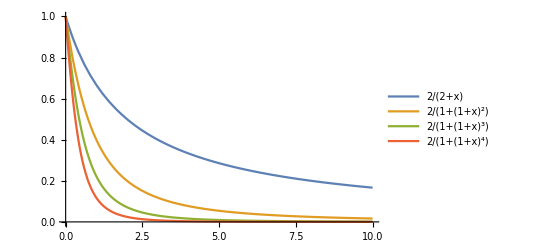

```mathematica
Plot[funcsShiftA,{x,0,10},PlotRange->{{0,10},{0,1}},PlotLegends->"Expressions"]
```

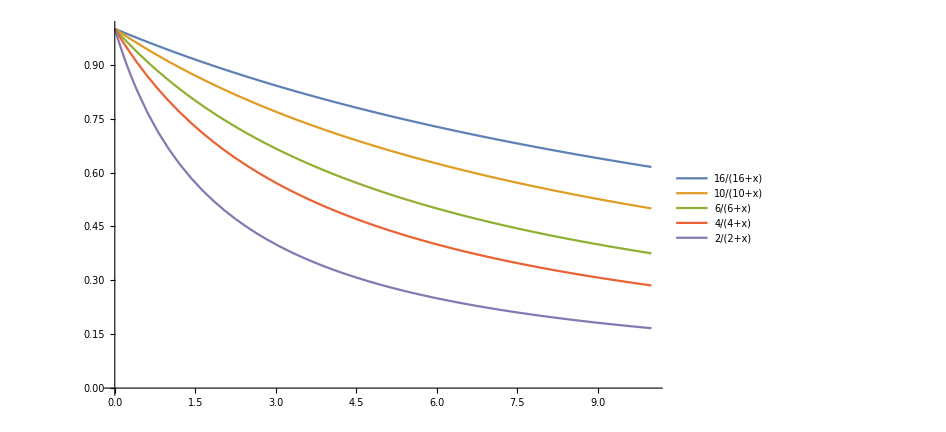

```mathematica
Plot[funcsShiftB1,{x,0,10},PlotRange->{{0,10},{0,1}},PlotLegends->"Expressions",ImageSize->700]
```

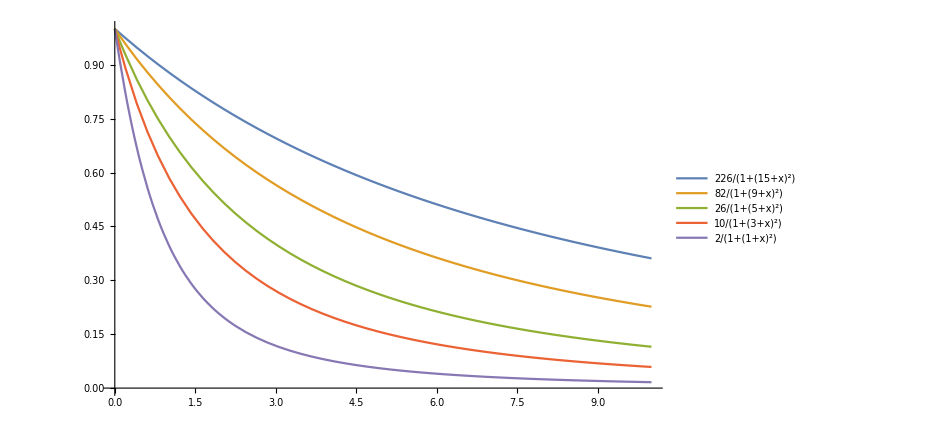

```mathematica
Plot[funcsShiftB2,{x,0,10},PlotRange->{{0,10},{0,1}},PlotLegends->"Expressions",ImageSize->700]
```

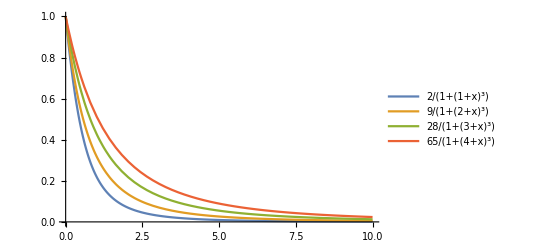

```mathematica
Plot[funcsShiftB3,{x,0,10},PlotRange->{{0,10},{0,1}},PlotLegends->"Expressions"]
```

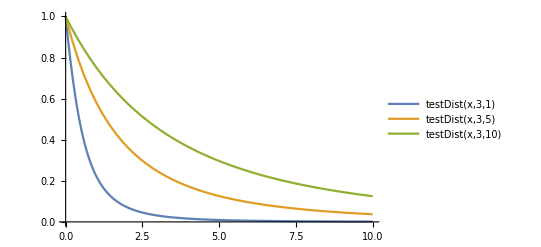

```mathematica
Plot[{testDist[x,3,1],testDist[x,3,5],testDist[x,3,10]},{x,0,10},PlotRange->{{0,10},{0,1}},PlotLegends->"Expressions"]
```

```mathematica
result=Solve[testDist[x,a,b]==c,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-b+(-(-1-b^a+c)/c)^(1/a)}}

```mathematica
result/.{b->2,c->57/100,a->4}//N
```

{{x→0.317078}}

## Plot ‘em all (in terms of RB)

```mathematica
RBPlotRange={{1,10},{0,1}};
```

```mathematica
RBPlotRangeMid={{1,100},{0,1}};
```

```mathematica
RBPlotRangeExt={{1,1000},{0,1}};
```

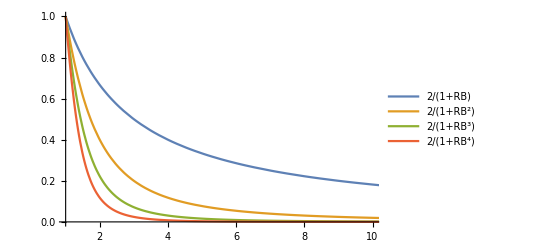

```mathematica
Plot[funcsShiftARB,{RB,1,100},PlotRange->RBPlotRange,PlotLegends->"Expressions"]
```

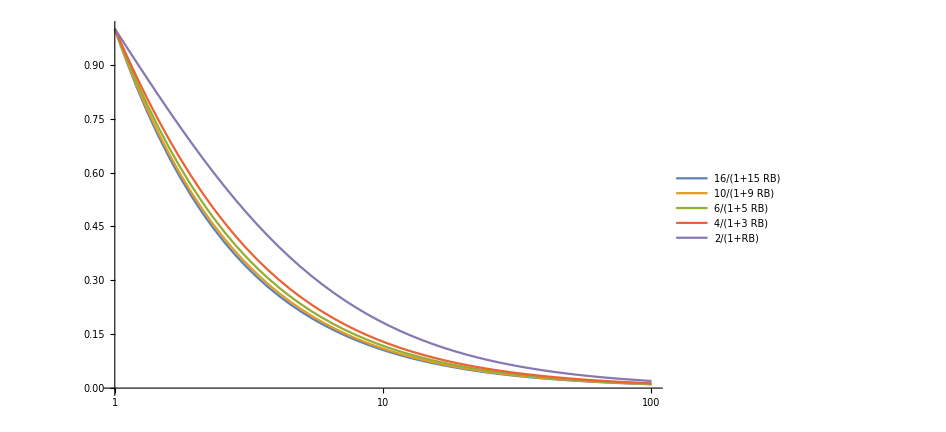

```mathematica
LogLinearPlot[funcsShiftB1RB,{RB,1,100},PlotRange->RBPlotRangeMid,PlotLegends->"Expressions",ImageSize->700]
```

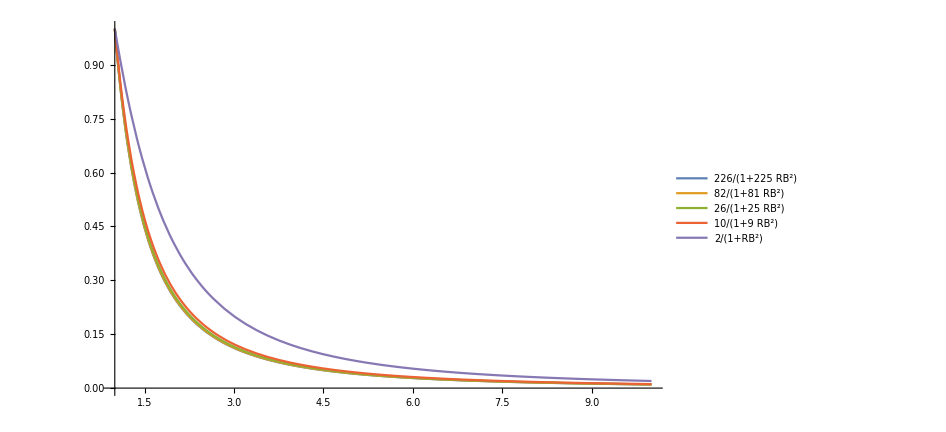

```mathematica
Plot[funcsShiftB2RB,{RB,1,10},PlotRange->RBPlotRange,PlotLegends->"Expressions",ImageSize->700]
```

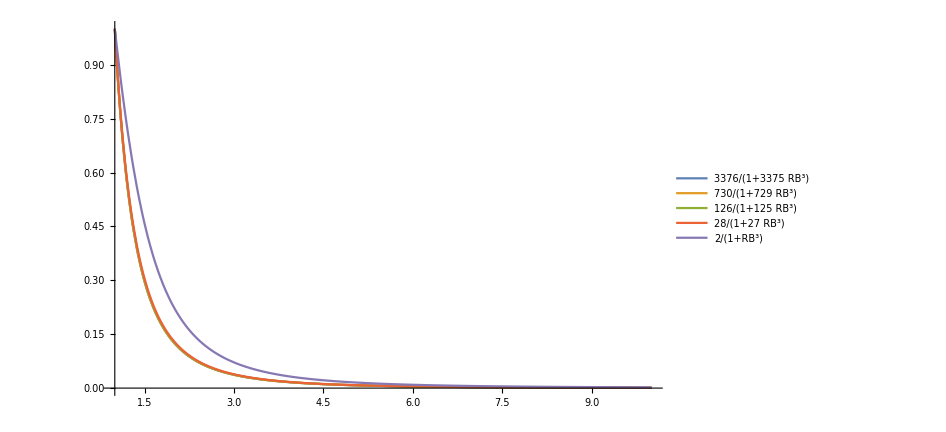

```mathematica
Plot[funcsShiftB3RB,{RB,1,10},PlotRange->RBPlotRange,PlotLegends->"Expressions",ImageSize->700]
```

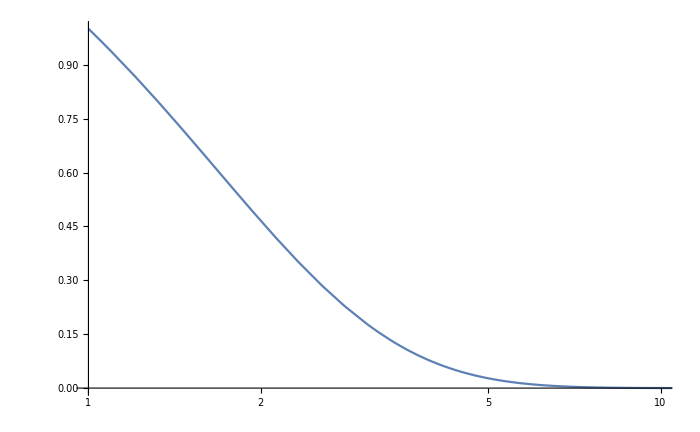

```mathematica
LogLinearPlot[testDistRBExp[RB,1,2],{RB,1,100},PlotRange->RBPlotRange,PlotLegends->"Expressions",ImageSize->700]
```

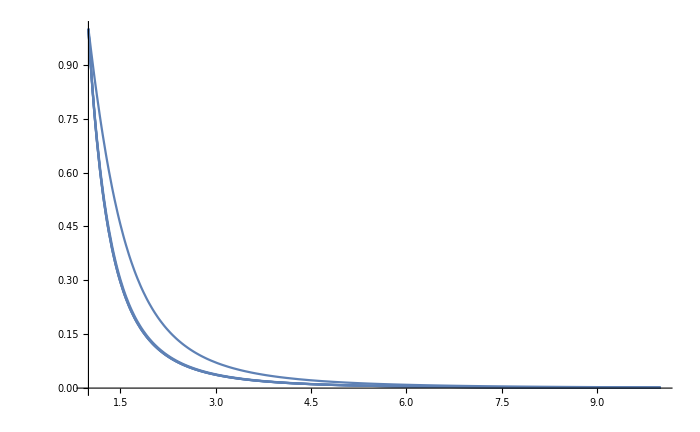

```mathematica
Plot[funcsShiftBARB[3],{RB,1,10},PlotRange->RBPlotRange,PlotLegends->"Expressions",ImageSize->700]
```

```mathematica
resultRB=Solve[testDistRB[RB,a,b]==c,RB]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{RB→(-(b^-a (-1-b^a+c))/c)^(1/a)}}

```mathematica
potAbove=941;potTot=2000;
```

```mathematica
(potTot-potAbove)/potTot//N
```

0.5295

```mathematica
resultRB/.{b->0.5,c->(potTot-potAbove)/potTot,a->0.5}//N
```

{{RB→9.89233}}

```mathematica
4*19.28
```

77.12

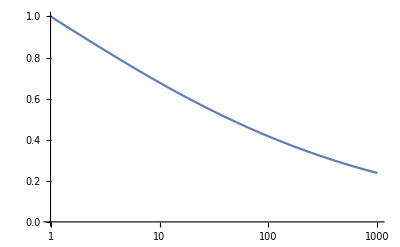

```mathematica
LogLinearPlot[testDistRB[RB,0.29,1],{RB,1,1000},PlotRange->RBPlotRangeExt]
```

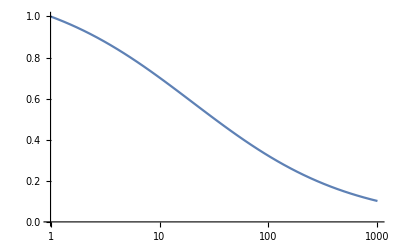

```mathematica
LogLinearPlot[testDistRB[RB,0.6,0.05],{RB,1,1000},PlotRange->RBPlotRangeExt]
```

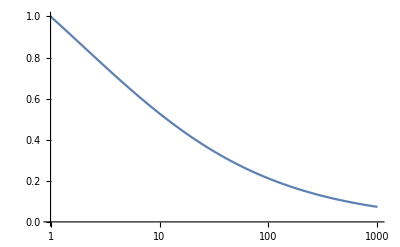

```mathematica
LogLinearPlot[testDistRB[RB,0.5,0.5],{RB,1,1000},PlotRange->RBPlotRangeExt]
```

## None of these seem to be working ... Try exponential, you suppose?

```mathematica
Exp/@-{0.1,0.2,0.3,0.4,0.5,0.55,0.56,0.567143}//N
```

{0.904837,0.818731,0.740818,0.67032,0.606531,0.57695,0.571209,0.567143}

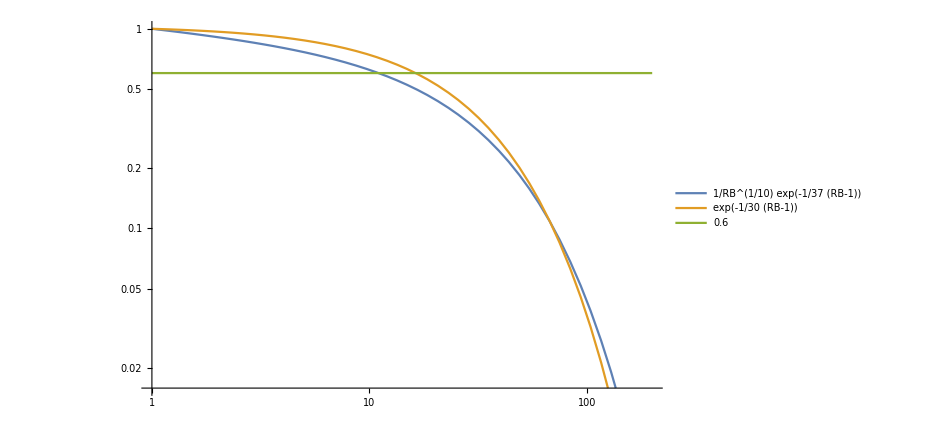

```mathematica
LogLogPlot[{RB^(-1/10) Exp[-1/37(RB-1)], Exp[-1/30(RB-1)],0.6},{RB,1,200},ImageSize->700,PlotLegends->"Expressions"]
```

Man, it barely does the job

```mathematica
Exp[-19/30]//N
```

0.530819

## So now define distribution funcs

## Distribution functions at source

#### Step function definition

```mathematica
sourcePieceFunc[vpar_,vperp_,vbth_,RB_]:=Piecewise[{{1,Im[Sqrt[vperp^2(1-RB)+vpar^2+vbth^2(1-Exp[-1/30(RB-1)])]]==0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-RB)+vpar^2+vbth^2≤ 0}}]
```

#### Kappa and Maxwellian functions at source assumes Π(R_B= 1) = 0

```mathematica
sourceFuncMaxwellian[vpar0_,vperp0_,vbth0_,RB_]:=1/π^(3/2)Exp[-(vpar0^2+vperp0^2)]sourcePieceFunc[vpar0,vperp0,vbth0,RB]
```

```mathematica
sourceFuncKappa[vpar0_,vperp0_,vbth0_,RB_,kappa_]:=1/(π^(3/2)(1-3/(2 kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(vpar0^2+vperp0^2)/(kappa-3/2))^(-(kappa+1))sourcePieceFunc[vpar0,vperp0,vbth0,RB]
```

```mathematica
midFuncMaxwellian[vpar_,vperp_,vbth0_,RB_]:=1/π^(3/2)Exp[-(vpar^2+vperp^2+vbth0^2(Exp[-1/30(RB-1)]-1))]UnitStep[vpar](*sourcePieceFunc[vpar0,vperp0,vbth0,RB]*)
```

```mathematica
midFuncKappa[vpar_,vperp_,vbth0_,RB_,kappa_]:=1/(π^(3/2)(1-3/(2 kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(vpar^2+vperp^2+vbth0^2(Exp[-1/30(RB-1)]-1))/(kappa-3/2))^(-(kappa+1))UnitStep[vpar](*sourcePieceFunc[vpar0,vperp0,vbth0,RB]*)
```

#### Put all the accel toward vPar (lots of garbage

```mathematica
(*midFuncKappa[vpar_,vperp_,vbth0_,RB_,kappa_]:=1/(π^(3/2)(1-3/(2 kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+((vpar-vbth0 Sqrt[1-Exp[-1/30(RB-1)]])^2+vperp^2 RB)/(kappa-3/2))^(-(kappa+1))UnitStep[vpar](*sourcePieceFunc[vpar0,vperp0,vbth0,RB]*)*)
```

Whole new thang (but garbage in retrospect)

```mathematica
(*midFuncMaxwellian[vpar_,vperp_,vbth0_,RB_]:=1/π^(3/2)Exp[-((vpar-vbth0(1-Exp[-1/30(RB-1)])^(1/2))^2+vperp^2 RB)](*sourcePieceFunc[vpar0,vperp0,vbth0,RB]*)*)
```

… And a whole new thang (but in retrospect, garbage!)

```mathematica
(*midFuncMaxwellian[vpar_,vperp_,vbth0_,alpha_]:=1/π^(3/2)Exp[-(vperp^2+vpar^2+vbth0^2(1-Exp[-1/30(1/alpha-1)])-2 vbth0(1-Exp[-1/30(1/alpha-1)])^(1/2)(vpar^2+(1-alpha)vperp^2)^(1/2))]UnitStep[vpar](*sourcePieceFunc[vpar0,vperp0,vbth0,RB]*)*)
```

… Der neueste!

```mathematica
midFuncMaxwellian[vpar_,vperp_,vbth0_,alpha_]:=1/π^(3/2)Exp[-(vperp^2+vpar^2-2 vbth0(1-Exp[-1/30(1/alpha-1)])^(1/2)(vpar^2+(1-alpha)vperp^2-vbth0^2(1-Exp[-1/30(1/alpha-1)]))^(1/2))]UnitStep[vpar](*sourcePieceFunc[vpar0,vperp0,vbth0,RB]*)
```

```mathematica
vbthK[dPhi_,Tm_,kappa_]:=√(dPhi/(Tm(1-3/(2 kappa))));
vbth[dPhi_,Tm_]:=√(dPhi/Tm);
```

### Dist. functions in cylindrical coordinates

```mathematica
midFuncMaxwellCyl[rho_,phi_,vbth_,alpha_]:=2/(√π)Exp[-(rho^2-2 vbth(1-Exp[-1/30(1/alpha-1)])^(1/2)(rho^2(1-alpha (Sin[phi])^2)-vbth^2(1-Exp[-1/30(1/alpha-1)]))^(1/2))];
midFuncMaxwellCylUnitStep[rho_,phi_,vbth_,alpha_]:=2/(√π)Exp[-(rho^2-2 vbth(1-Exp[-1/30(1/alpha-1)])^(1/2)(rho^2(1-alpha (Sin[phi])^2)-vbth^2(1-Exp[-1/30(1/alpha-1)]))^(1/2))]UnitStep[rho^2(1-alpha(Sin[phi])^2)-vbth^2(1-Exp[-1/30(1/alpha-1)])];
```

```mathematica
midFuncKappaCyl[rho_,phi_,vbth_,alpha_,kappa_]:=2/(√π(1-3/(2kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(rho^2-2 vbth(1-Exp[-1/30(1/alpha-1)])^(1/2)(rho^2(1-alpha (Sin[phi])^2)-vbth^2(1-Exp[-1/30(1/alpha-1)]))^(1/2))/(kappa-3/2))^(-(kappa+1))
```

```mathematica
midFuncKappaCylUnitStep[rho_,phi_,vbth_,alpha_,kappa_]:=2/(√π(1-3/(2kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(rho^2-2 vbth(1-Exp[-1/30(1/alpha-1)])^(1/2)(rho^2(1-alpha (Sin[phi])^2)-vbth^2(1-Exp[-1/30(1/alpha-1)]))^(1/2))/(kappa-3/2))^(-(kappa+1))UnitStep[rho^2(1-alpha(Sin[phi])^2)-vbth^2(1-Exp[-1/30(1/alpha-1)])];
```

## Distribution Function Plots (looks nice, the mapping is reaaal nice)

```mathematica
vbthTot=√(2200/110)//N
```

4.47214

### Function at source, with lines showing which particles make it to the bottom (I think)

```mathematica
Manipulate[Plot3D[sourceFuncKappa[vpar,vperp,vbth,RB,kappa],{vpar,0,3},{vperp,-1.5,1.5},PlotRange->Full,ImageSize->700],{RB,{1,3/2,2,5/2,3,10,30,50,70,100,200,300,500,700,1000}},{vbth,0,5},{{kappa,2},3/2,10}]
```

### Function along field line

```mathematica
Manipulate[Plot3D[midFuncMaxwellian[vpar,vperp,vbth,alpha],{vpar,0,10},{vperp,-6,6},PlotRange->Full,ImageSize->700,PlotPoints->50],{alpha,1/{1,3/2,2,5/2,3,10,30,50,70,100,200,300,500,700,1000}},{{vbth,vbthTot},0,5}]
```

### Parametric kappa plot

```mathematica
dPhiTot=2200;Tm=110;kaps=18/10;
```

```mathematica
Manipulate[ParametricPlot3D[{rho Cos[phi],rho Sin[phi],midFuncKappaCyl[rho,phi,vbth[dPhiTot,Tm],alpha,kaps]},{rho,minRhoInteg,maxRhoInteg},{phi,-π/2,π/2},PlotRange->All,PlotPoints->50,ImageSize->800],{{alpha,125/10000},0,1}]
```

ParametricPlot3D::plln: Limiting value minRhoInteg in {rho,minRhoInteg,maxRhoInteg} is not a machine-sized real number.

```mathematica
ParametricPlot3D[{rho Cos[phi],rho Sin[phi],midFuncMaxwellCyl[rho,phi,vbth[dPhiTot,Tm],0.05]},{rho,0,6},{phi,-π/2,π/2},PlotRange->All,PlotPoints->20,ImageSize->800]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{rho Cos[phi],rho Sin[phi],midFuncMaxwellCyl[rho,phi,vbth[dPhiTot,Tm],0.0125]},{rho,0,8},{phi,-π/2,π/2},PlotRange->All,PlotPoints->20,ImageSize->800]
```

-Graphics3D-

## Tons of NIntegration

```mathematica
dPhiTot=2200;Tm=110;kaps=18/10;
```

### Tons of baby lil’ Maxwellian NIntegrates

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhiTot,Tm],1/2],{rho,0,6},{phi,0,π/2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {1.14512,1.5617276690338959023451881336086444207467138767242431640625}. NIntegrate obtained 1.39774 and 0.0000187616 for the integral and error estimates.

1.39774

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhiTot,Tm],1],{rho,0,6},{phi,0,π/2}]
```

0.5

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhiTot,Tm],1/3],{rho,0,6},{phi,0,π/2}]
```

2.13056

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhiTot,Tm],1/4],{rho,0,6},{phi,0,π/2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {1.59208,1.510961155740288629212297877302262349985539913177490234375}. NIntegrate obtained 3.03344 and 5.50678×10^-6 for the integral and error estimates.

3.03344

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhiTot,Tm],1/5],{rho,0,6},{phi,0,π/2}]
```

3.79897

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhiTot,Tm],1/7],{rho,0,6},{phi,0,π/2}]
```

5.42184

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhiTot,Tm],1/8],{rho,0,6},{phi,0,π/2}]
```

6.21512

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhiTot,Tm],1/10],{rho,0,6},{phi,0,π/2}]
```

7.76774

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhiTot,Tm],1/15],{rho,0,6},{phi,0,π/2}]
```

11.4621

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhiTot,Tm],1/18],{rho,0,6},{phi,0,π/2}]
```

13.5422

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhiTot,Tm],1/20],{rho,0,6},{phi,0,π/2}]
```

14.8581

```mathematica
(NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhiTot,Tm],#],{rho,0,12},{phi,0,π/2}])&/@{1/20,1/25,1/30,1/40,1/50,1/60,1/70,1/80}
```

{14.9091,18.1004,21.0427,26.2137,30.5141,34.0598,36.9702,39.357}

```mathematica
(NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhiTot,Tm],#],{rho,0,12},{phi,0,π/2}])&/@{1/100,1/200,1/300,1/500,1/700,1/1000,1/2000}
```

{42.9361,50.2171,52.5386,54.4421,55.2817,55.9215,56.6788}

### Tons of baby lil’ kappa NIntegrates

```mathematica
alphaList={1,1/2,1/3,1/4,1/5,1/7,1/8,1/10,1/15,1/18,1/20,1/25,1/30,1/40,1/50,1/60,1/70,1/80,1/90,1/100,1/130,1/170,1/200,1/250,1/300,1/400,1/500,1/600,1/700,1/800,1/1000,1/1500,1/2000,1/3000};
```

```mathematica
RBList=1/alphaList
```

{1,2,3,4,5,7,8,10,15,18,20,25,30,40,50,60,70,80,90,100,130,170,200,250,300,400,500,600,700,800,1000,1500,2000,3000}

```mathematica
minRhoInteg=0;maxRhoInteg=12;
```

```mathematica
MaxwellIntegList = (NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhiTot,Tm],#],{rho,minRhoInteg,maxRhoInteg},{phi,0,π/2}])&/@ alphaList
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {1.14513,1.5617276690338959023451881336086444207467138767242431640625}. NIntegrate obtained 1.39774 and 0.0000187607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {1.5915,1.49406112316176013787849541358809801749885082244873046875}. NIntegrate obtained 3.03344 and 0.0000128962 for the integral and error estimates.

{0.5,1.39774,2.13056,3.03344,3.79897,5.42184,6.21513,7.76779,11.4655,13.562,14.9091,18.1004,21.0427,26.2137,30.5141,34.0598,36.9702,39.357,41.318,42.9361,46.3502,48.9742,50.2171,51.6084,52.5386,53.7197,54.4421,54.9301,55.2817,55.5472,55.9215,56.425,56.6788,56.9339}

```mathematica
kappaEq1p6=(NIntegrate[rho^2 Sin[phi] midFuncKappaCylUnitStep[rho,phi,vbth[dPhiTot,Tm],#,16/10],{rho,minRhoInteg,maxRhoInteg},{phi,0,π/2}])&/@alphaList
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {1.14513,1.5617276690338959023451881336086444207467138767242431640625}. NIntegrate obtained 1.43038 and 4.44477×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.499742,1.43038,2.12701,2.96125,3.71271,5.23944,6.00119,7.52512,11.3429,13.6397,15.1733,19.0152,22.8661,30.5847,38.3069,46.0099,53.6713,61.2709,68.7906,76.2154,97.8105,124.803,143.644,172.486,198.397,242.762,279.132,309.362,334.826,356.539,391.545,448.971,483.657,523.434}

```mathematica
kappaEq1p8=(NIntegrate[rho^2 Sin[phi] midFuncKappaCylUnitStep[rho,phi,vbth[dPhiTot,Tm],#,18/10],{rho,minRhoInteg,maxRhoInteg},{phi,0,π/2},WorkingPrecision->13])&/@alphaList
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.4997359741712,1.431174726591,2.129498322782,3.018620187634,3.786594936251,5.36857658306,6.154697593238,7.723445884197,11.63370802487,13.97207282388,15.5270066949,19.39702804809,23.23635931494,30.79391046454,38.14500455888,45.24734931237,52.06607909037,58.58087674595,64.78134698602,70.66587499217,86.501995665,103.9118218472,114.743878219,129.609262026,141.5005437922,159.3028208905,171.9665226916,181.4215425357,188.7444683696,194.580848576,203.2952050677,216.0140820591,222.8998222511,230.1729210743}

```mathematica
kappaEq2=(NIntegrate[rho^2 Sin[phi] midFuncKappaCylUnitStep[rho,phi,vbth[dPhiTot,Tm],#,2],{rho,minRhoInteg,maxRhoInteg},{phi,0,π/2}])&/@alphaList
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {1.14513,1.5617276690338959023451881336086444207467138767242431640625}. NIntegrate obtained 1.42802 and 0.0000113319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {1.59301,1.56238406238233133727089096964846248738467693328857421875}. NIntegrate obtained 3.03522 and 4.61727×10^-6 for the integral and error estimates.

{0.499827,1.42802,2.1319,3.03522,3.80701,5.40784,6.20115,7.78063,11.6979,14.0265,15.5686,19.3835,23.1329,30.3993,37.3079,43.8187,49.9109,55.5808,60.838,65.7012,78.1885,90.9635,98.4573,108.241,115.695,126.307,133.494,138.679,142.595,145.656,150.132,156.47,159.81,163.272}

```mathematica
kappaEq3=(NIntegrate[rho^2 Sin[phi] midFuncKappaCylUnitStep[rho,phi,vbth[dPhiTot,Tm],#,3],{rho,minRhoInteg,maxRhoInteg},{phi,0,π/2}])&/@alphaList
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {1.14513,1.5617276690338959023451881336086444207467138767242431640625}. NIntegrate obtained 1.41613 and 0.0000154998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {1.5915,1.49406112316176013787849541358809801749885082244873046875}. NIntegrate obtained 3.04558 and 7.79827×10^-6 for the integral and error estimates.

{0.499989,1.41613,2.13423,3.04558,3.81757,5.43777,6.23566,7.81395,11.67,13.9216,15.3954,18.9793,22.4119,28.7975,34.5283,39.6179,44.1051,48.0444,51.4966,54.5231,61.6001,67.9151,71.2524,75.2749,78.1264,81.9189,84.3308,86.0001,87.2237,88.1591,89.4947,91.3244,92.2609,93.2121}

### Yeah whatever, now make some plots

```mathematica
MaxwellPlotList=Partition[Riffle[RBList,MaxwellIntegList],2]
```

{{1,0.5},{2,1.39774},{3,2.13056},{4,3.03344},{5,3.79897},{7,5.42184},{8,6.21513},{10,7.76779},{15,11.4655},{18,13.562},{20,14.9091},{25,18.1004},{30,21.0427},{40,26.2137},{50,30.5141},{60,34.0598},{70,36.9702},{80,39.357},{90,41.318},{100,42.9361},{130,46.3502},{170,48.9742},{200,50.2171},{250,51.6084},{300,52.5386},{400,53.7197},{500,54.4421},{600,54.9301},{700,55.2817},{800,55.5472},{1000,55.9215},{1500,56.425},{2000,56.6788},{3000,56.9339}}

```mathematica
kappaEq1p6PlotList=Partition[Riffle[RBList,kappaEq1p6],2]
```

{{1,0.499742},{2,1.43038},{3,2.12701},{4,2.96125},{5,3.71271},{7,5.23944},{8,6.00119},{10,7.52512},{15,11.3429},{18,13.6397},{20,15.1733},{25,19.0152},{30,22.8661},{40,30.5847},{50,38.3069},{60,46.0099},{70,53.6713},{80,61.2709},{90,68.7906},{100,76.2154},{130,97.8105},{170,124.803},{200,143.644},{250,172.486},{300,198.397},{400,242.762},{500,279.132},{600,309.362},{700,334.826},{800,356.539},{1000,391.545},{1500,448.971},{2000,483.657},{3000,523.434}}

```mathematica
kappaEq1p8PlotList=Partition[Riffle[RBList,kappaEq1p8],2]
```

{{1,0.499736},{2,1.43117},{3,2.1295},{4,3.01862},{5,3.7866},{7,5.36858},{8,6.1547},{10,7.72344},{15,11.6337},{18,13.9721},{20,15.527},{25,19.397},{30,23.2364},{40,30.794},{50,38.1457},{60,45.2473},{70,52.0661},{80,58.5809},{90,64.7813},{100,70.6658},{130,86.5019},{170,103.912},{200,114.744},{250,129.609},{300,141.5},{400,159.303},{500,171.966},{600,181.421},{700,188.744},{800,194.581},{1000,203.295},{1500,216.014},{2000,222.9},{3000,230.173}}

```mathematica
kappaEq2PlotList=Partition[Riffle[RBList,kappaEq2],2]
```

{{1,0.499827},{2,1.42802},{3,2.1319},{4,3.03522},{5,3.80701},{7,5.40784},{8,6.20115},{10,7.78063},{15,11.6979},{18,14.0265},{20,15.5686},{25,19.3835},{30,23.1329},{40,30.3993},{50,37.3079},{60,43.8187},{70,49.9109},{80,55.5808},{90,60.838},{100,65.7012},{130,78.1885},{170,90.9635},{200,98.4573},{250,108.241},{300,115.695},{400,126.307},{500,133.494},{600,138.679},{700,142.595},{800,145.656},{1000,150.132},{1500,156.47},{2000,159.81},{3000,163.272}}

```mathematica
kappaEq3PlotList=Partition[Riffle[RBList,kappaEq3],2]
```

{{1,0.499989},{2,1.41613},{3,2.13423},{4,3.04558},{5,3.81757},{7,5.43777},{8,6.23566},{10,7.81395},{15,11.67},{18,13.9216},{20,15.3954},{25,18.9793},{30,22.4119},{40,28.7975},{50,34.5283},{60,39.6179},{70,44.1051},{80,48.0444},{90,51.4966},{100,54.5231},{130,61.6001},{170,67.9151},{200,71.2524},{250,75.2749},{300,78.1264},{400,81.9189},{500,84.3308},{600,86.0001},{700,87.2237},{800,88.1591},{1000,89.4947},{1500,91.3244},{2000,92.2609},{3000,93.2121}}

### Plots of ze results

```mathematica
nDigitsdPhi=3;nDigitsTm=3;
```

#### Full range

```mathematica
legendStyles=(Style[#,18])&/@{"κ = 1.6","κ = 1.8","κ = 2","κ = 3","Maxwellian"}
```

{κ = 1.6,κ = 1.8,κ = 2,κ = 3,Maxwellian}

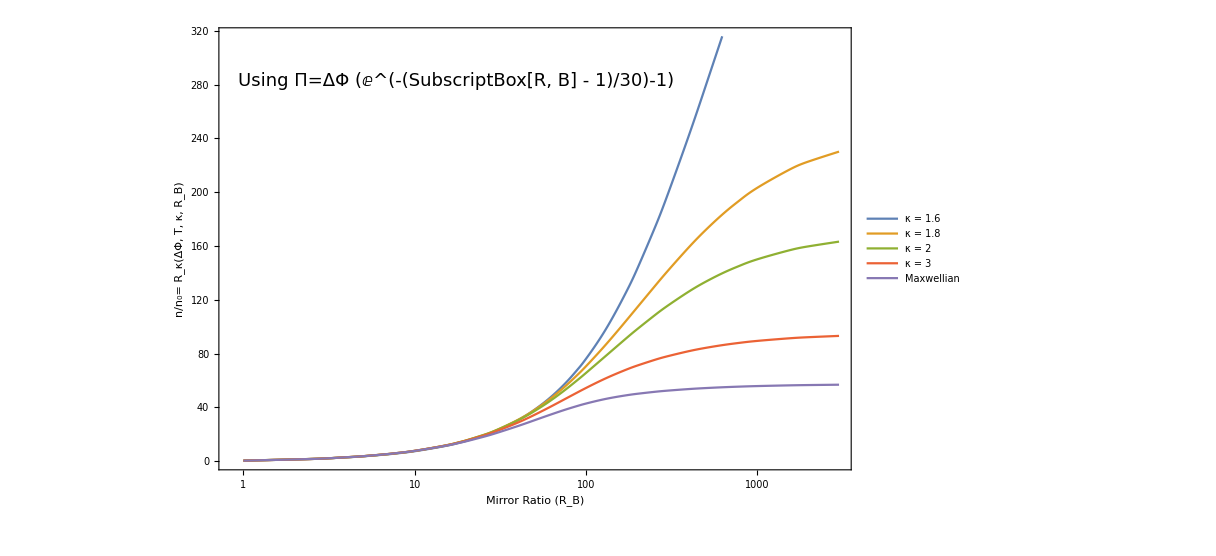

```mathematica
ListLogLinearPlot[{kappaEq1p6PlotList,kappaEq1p8PlotList,kappaEq2PlotList,kappaEq3PlotList,MaxwellPlotList},Joined->True,InterpolationOrder->3,PlotLegends->legendStyles,Frame->True,FrameStyle->Directive[Black,(FontSize->19)],PlotStyle->Directive[(FontSize->19)],FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio (R_B)"],StringForm["ΔΦ = `1` V; T_m = `2` eV; ϕ̄ = `3`",NumberForm[dPhiTot,nDigitsdPhi],NumberForm[Tm,nDigitsTm],NumberForm[N[dPhiTot/Tm],{3,1}]]}},Epilog->{Text[Style["Using Π=ΔΦ (ⅇ^(-(SubscriptBox[R, B] - 1)/30)-1)",18],Scaled[{0.03,0.9}],{-1,1}]},ImageSize->900]
```

#### Adjusted range

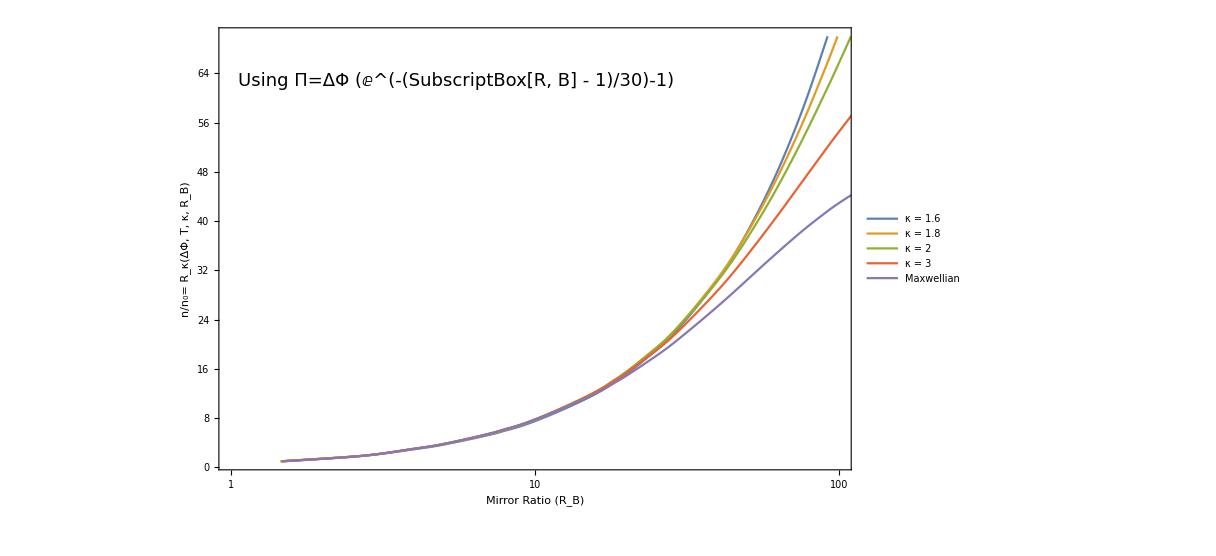

```mathematica
ListLogLinearPlot[{kappaEq1p6PlotList,kappaEq1p8PlotList,kappaEq2PlotList,kappaEq3PlotList,MaxwellPlotList},PlotRange->{{1,100},{1,70}},Joined->True,InterpolationOrder->3,PlotLegends->legendStyles,Frame->True,FrameStyle->Directive[Black,(FontSize->19)],PlotStyle->Directive[(FontSize->19)],FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio (R_B)"],StringForm["ΔΦ = `1` V; T_m = `2` eV; ϕ̄ = `3`",NumberForm[dPhiTot,nDigitsdPhi],NumberForm[Tm,nDigitsTm],NumberForm[N[dPhiTot/Tm],{3,1}]]}},Epilog->{Text[Style["Using Π=ΔΦ (ⅇ^(-(SubscriptBox[R, B] - 1)/30)-1)",18],Scaled[{0.03,0.9}],{-1,1}]},ImageSize->900]
```